## Wechat Chat History Tools

Version 2.1:
2017-6-23
Added message sender individual counts.
Reorganized the notebook.
Version 2:
Database format based on the newest version as of 2016 Dec
If you receive lots of errors, it is likely that the database format has changed again, since this has happened before.

User manual: evaluate all cells in the given order, change the information specified. You can ignore the comments in code.

### Initialization code

```mathematica
Needs["DatabaseLink`"];
loadWechatDatabase[mmpath_,contpath_]:=Module[{},
(*I did not block any symbols, they can be used after words*)
mmConn=OpenSQLConnection[JDBC["SQLite",mmpath]];
contConn=OpenSQLConnection[JDBC["SQLite",contpath]];rawcontact=SQLSelect[contConn,"Friend"];(*01 is male, 02 is female, 00 is unknown*)
contact=readContact/@rawcontact[[All,{1,8,10}]]//Quiet;
chatID="Chat_"<>IntegerString[Hash[#,"MD5"],16,32]&/@(Transpose[contact])[[1]];getInfo=AssociationThread[chatID,contact];availChatID=Select[SQLTableNames[mmConn],StringContainsQ[#,"Chat_"]&];availUserInfo=Lookup[getInfo,availChatID];chatData=(SQLSelect[mmConn,#]&/@availChatID)[[All,All,{4,5,9}]];(*since order is preserved, any other info than time is useless for counting, improves performance*)(*but to analysis contents, use full database chatData instead*)chatTimeStamps=chatData[[All,All,1]];
]
(*the function does not handle emoji in names because MMA does not support it*)
(*shortest pattern to match username, nickname, internalID, has issues, eats first letter of user defined ID occasionally*)readContact[{username_,SQLBinary[{Longest[x__]/;Length[{x}]>1,18,y__,26,z__,34,___}],profile_}]:={username,Sequence@@(FromCharacterCode[#,"UTF-8"]&/@{Drop[{x},2],Drop[{y},1],Drop[{z},1]}),profile[[1,2]]};
readContact[___]:=Nothing;
(*the time stamp is the second elapsed from 1970-1-1 8:00AM (GMT+8)*)
(*convert time to date string, for output*)
toDateString=DateString@AbsoluteTime[2209017600+#]&;
(*convert date string to internal time, for selection*)
toInternalTime=AbsoluteTime[#]-2209017600&;
(*all message counts*)
topAllChatCounts[anydb_]:=Transpose[{Length/@anydb,availUserInfo}]//Sort//Reverse;
(*note: be aware of the precedence of the Alternative operator in string patterns*)
noGroups[countRes_]:=countRes/.{__,{_?(StringQ[#]&&StringMatchQ[#,(__~~"@chatroom")|("gh_"~~__)]&),__}}:>Nothing;
(*2.1 new: displays count of message sent by user and others in a chat*)
(*0 represents the user, and 1 presents other(s)(this 's' refers to a group chat) in a chat*)
(*unlike the previous count functions, this functions must take the full chat variable as the argument*)
topAllChatIndividualCounts[fulldb_]:=Transpose[{Length/@fulldb,Tally/@fulldb[[All,All,-1]],availUserInfo}]//Sort//Reverse;
(*performs counting over a specific time range*)
(*function takes two DateObjects*)
takeTimeStampRange[timestampdb_,start_,end_]:=With[{s=toInternalTime[start],e=toInternalTime[end]},Select[s≤#≤e&]/@timestampdb];
takeTimeRange[fulldb_,start_,end_]:=With[{s=toInternalTime[start],e=toInternalTime[end]},Select[s≤#[[1]]≤e&]/@fulldb];
(*generate a random time range*)
randomDateRange[timestampdb_]:=Module[{lowerlim,upperlim},{lowerlim,upperlim}=MinMax@Flatten@timestampdb;DateObject/@Sort@RandomInteger[{lowerlim,upperlim}+2209017600,2]];
(*get chat data for a specfic user by internalID*)
userChat[fulldb_,id_String]:=Position[availUserInfo,id]//Flatten//First//fulldb[[#]]&;
(*distribution of messages over time*)
toTimeSeries[singledb_,period:("Week"|"Month")]:=Module[{firstDay,lastDay,timedomain,counts},{firstDay,lastDay}=MinMax[Flatten@singledb[[All,1]]+2209017600];timedomain=DateRange[DateObject[firstDay],DateObject[lastDay], {1,period}];counts=BinLists[singledb[[All,1]],{AbsoluteTime/@timedomain-2209017600}]//Length/@#&;Transpose[{timedomain[[;;-2]],counts}]
];
(*unfortunately, excel format does not have that may rows to store all chats*)
(*Export["chat_history.xlsx",Thread[availUserInfo[[All,2]]->chatData]]*)
exportAllHistory[filename_]:=Export[filename,Join@@(Level[#,{-2}]&/@Transpose[{availUserInfo,MapAt[toDateString,chatData[[All,All,{1,3,2}]],{All,All,1}]}])]//AbsoluteTiming;
```

Change the following paths to the two sqlite files according to README

Run the following code to preprocess the chat database

```mathematica
mmPath="/Users/vaporized/Desktop/wechat_backups/2017623_full/DB/MM.sqlite";
contactPath="/Users/vaporized/Desktop/wechat_backups/2017623_full/DB/WCDB_Contact.sqlite";
loadWechatDatabase[mmPath,contactPath];
```

### All message counts

```mathematica
(*include groups and subscriptions, first 20*)
top20All=topAllChatCounts[chatTimeStamps]//Take[#,UpTo[20]]&;
(*for privacy reasons, only message counts are displayed as a public example. But the variable top20All will contain all infomation in your run*)
top20All[[All,1]]
```

{87023,43647,35583,35516,27605,25679,23447,19385,18863,18822,18792,13894,13805,11480,10004,7870,7071,6733,5628,5147}

```mathematica
(*include groups and subscriptions, first 20, with individual message counts*)
(*0 represents the user*)
top20AllVerbose=topAllChatIndividualCounts[chatData]//Take[#,UpTo[20]]&;
(*for privacy reasons, only message counts are displayed as a public example. But the variable top20All will contain all infomation in your run*)
top20AllVerbose[[All,{1,2}]]
```

{{87023,{{1,53758},{0,33265}}},{43647,{{1,24031},{0,19616}}},{35583,{{1,18119},{0,17464}}},{35516,{{1,15568},{0,19948}}},{27605,{{1,26797},{0,808}}},{25679,{{1,12091},{0,13588}}},{23447,{{0,13182},{1,10265}}},{19385,{{1,8981},{0,10404}}},{18863,{{1,10005},{0,8858}}},{18822,{{1,18761},{0,61}}},{18792,{{0,7835},{1,10957}}},{13894,{{1,8919},{0,4975}}},{13805,{{1,7982},{0,5823}}},{11480,{{1,6216},{0,5264}}},{10004,{{1,9973},{0,31}}},{7870,{{0,4266},{1,3604}}},{7071,{{1,5332},{0,1739}}},{6733,{{1,3519},{0,3214}}},{5628,{{1,5033},{0,595}}},{5147,{{1,4133},{0,1014}}}}

```mathematica
(*exclude groups and subscriptions, first 20*)
top20=noGroups@topAllChatCounts[chatTimeStamps]//Take[#,UpTo[20]]&;
(*message counts only*)
top20[[All,1]]
```

{43647,35583,35516,25679,23447,19385,18863,13805,11480,6733,4228,3557,3169,2970,2558,2124,2073,1859,1680,1516}

### Message counts over a certain time range

```mathematica
(*generate a random time interval*)
{date1,date2}=randomDateRange[chatTimeStamps];
```

```mathematica
(*in practice, you may want to specify a time range manually, here is how to do it*)
(*suppose you want the start date (date1 variable) to be 2016-08-17, you can do*)
date1=DateObject["2016-08-17"]
```

Wed 17 Aug 2016

```mathematica
(*specify a date, to today*)
partialChatTimeStamp=takeTimeStampRange[chatTimeStamps,DateObject["2017-04-01"],Today];
top20partialts=noGroups@topAllChatCounts[partialChatTimeStamp]//Take[#,UpTo[20]]&;
(*individual counts*)
partialChat=takeTimeRange[chatData,DateObject["2017-04-01"],Today];
top20partial=noGroups@topAllChatIndividualCounts[partialChat]//Take[#,UpTo[20]]&;
top20partial[[All,{1,2}]]
```

{{33664,{{1,17196},{0,16468}}},{4710,{{1,2182},{0,2528}}},{3594,{{0,1944},{1,1650}}},{1727,{{1,1007},{0,720}}},{860,{{0,441},{1,419}}},{699,{{1,440},{0,259}}},{483,{{1,229},{0,254}}},{469,{{0,268},{1,201}}},{267,{{1,177},{0,90}}},{239,{{1,135},{0,104}}},{201,{{1,120},{0,81}}},{144,{{1,70},{0,74}}},{131,{{1,50},{0,81}}},{127,{{1,69},{0,58}}},{85,{{1,44},{0,41}}},{85,{{1,40},{0,45}}},{82,{{1,43},{0,39}}},{65,{{1,37},{0,28}}},{64,{{1,27},{0,37}}},{59,{{1,31},{0,28}}}}

### Analysis a single person

```mathematica
(*place the wechat id you want to analysis here, it is of form wxid_XXX..., you can get such information by evaluating `availUserInfo`*)
testid="wxid_XXXXXXXXXXXXXXX";
```

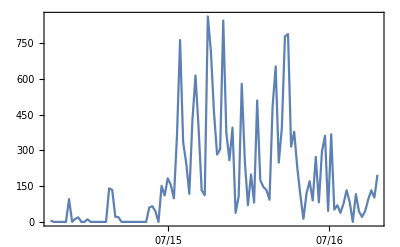

```mathematica
(*You can perform either a week or a month summation, by altering that "Week"/"Month"*)
(*in this picture, every datapoint(although they are connected) is a summation of week, the connection only shows the trend*)
DateListPlot[toTimeSeries[userChat[chatData,testid],"Week"],PlotRange->All,DateTicksFormat->{"Month", "/", "YearShort"}]
```

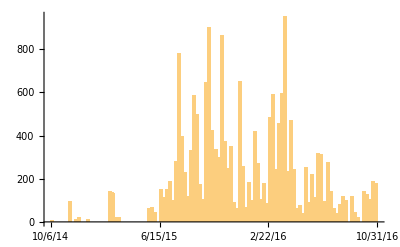

```mathematica
(*if you are not comfortable with the plot above, here is another option*)
DateHistogram[userChat[chatData,testid][[All,1]]+2209017600,"Week"]
```

### Export All Chat History as CSV

The file will be placed in your working directory if not specified.
Each line of chat data is of form: date string, sender(0 is yourself, 1 is the other, automatic specify person in groups), contents.
Different people/groups are separated by a line of user identity, it is of form: internal ID, name, user ID(if available), nickname(if available), gender.
Please note that exporting can take minutes if the database is large. And opening the CSV file with a professional text editor is strongly recommended, it can crash some editors that can’t handle big files.

```mathematica
exportAllHistory["history.csv"]
```

{131.888,history.csv}